```mathematica
(*Variables para modificar*)
np=5; (*numero de particulas*)
lg=8; (*limites del grafico cuadrado*)
pr=2.5; (*limite del grafico en eje z*)
```

```mathematica
(*Funciones de ayuda*)
ri:=RandomInteger[{- lg,lg}]
(*variable de valor diferido que funciona como funcion con un numero random de salida, ri es por Random Integer*)
rn:=RandomInteger[{1,4}];(*random natural; no se usa ri para no tener cargas iguales a 0*)

QRan:=Table[RandomChoice[{1,-1}]*rn,{np}];  (*genera una lista de cargas aleatorias*)

QIdn:=Table[RandomChoice[{-1,1}] * 4,{np}];(*Lista de cargas identicas*)
```

Correr la siguiente célula para generar nuevas partículas

```mathematica
BodyData={Table[{ri,ri},{np}],QRan}(*Datos de las particulas, con su pos. y car.*)
```

{{{-5,6},{3,8},{5,-5},{-7,-2},{1,7}},{2,-4,-2,3,3}}

Función para Calcular el Potencial en un Punto a Partir de Varias Cargas:
ϕ[r,Datos de Cuerpo]
Donde Datos de Cuerpo (o Body Data) contiene la posicion de las partículas en la primera sub-lista y las cargas en la segunda sub-lista

```mathematica
PotencialE[{x_,y_},BodyData_:BodyData]:=Table[ BodyData[[2]][[n]]/(4  π * Sqrt[(x-BodyData[[1]][[n]][[1]])^2+(y-BodyData[[1]][[n]][[2]])^2]^2) ,{n,Length@BodyData[[2]]}]//Total
PotencialE[{0,0}] (*Comprobando cuanto vale el potencial en el punto 
r={o,o}*)
```

644259/(47201800 π)

```mathematica
PotencialElectricoGrafico=Plot3D[PotencialE[{x,y},BodyData],{x,-lg,lg},{y,-lg,lg},ColorFunction->"BlueGreenYellow",Mesh->None,PlotLegends->Automatic,PlotRange->{- pr,pr}]
```

-Graphics3D-

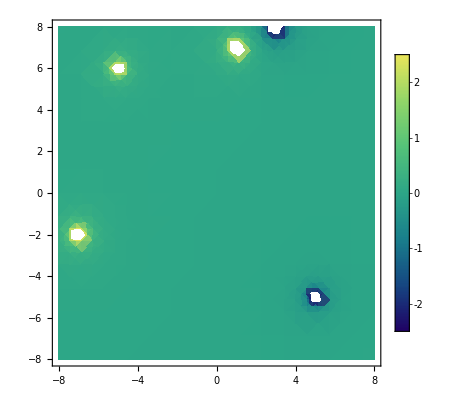

```mathematica
PEHeatG=DensityPlot[PotencialE[{x,y},BodyData],{x,-lg,lg},{y,-lg,lg},ColorFunction->"BlueGreenYellow",Mesh->None,PlotLegends->Automatic,PlotRange->{- pr,pr}]
```

```mathematica
PECP=ContourPlot[PotencialE[{x,y},BodyData],{x,-lg,lg},{y,-lg,lg},ContourStyle->White,ClippingStyle->Automatic,ContourShading->False]; (*el codigo de arriba es un grafico de contorno*)
```

El Campo Eléctrico es la derivada direccional del Potencial Electrostático
E = - ∇ϕ

```mathematica
CampoE=- Grad[PotencialE[{x,y},BodyData],{x,y}] (*Entrega una funcion, la cual puede utilizarse en graficas, plots...*)
```

{-(2 (-3+x))/(π ((-3+x)^2+(-8+y)^2)^2)+(3 (-1+x))/(2 π ((-1+x)^2+(-7+y)^2)^2)+(5+x)/(π ((5+x)^2+(-6+y)^2)^2)+(3 (7+x))/(2 π ((7+x)^2+(2+y)^2)^2)-(-5+x)/(π ((-5+x)^2+(5+y)^2)^2),-(2 (-8+y))/(π ((-3+x)^2+(-8+y)^2)^2)+(3 (-7+y))/(2 π ((-1+x)^2+(-7+y)^2)^2)+(-6+y)/(π ((5+x)^2+(-6+y)^2)^2)+(3 (2+y))/(2 π ((7+x)^2+(2+y)^2)^2)-(5+y)/(π ((-5+x)^2+(5+y)^2)^2)}

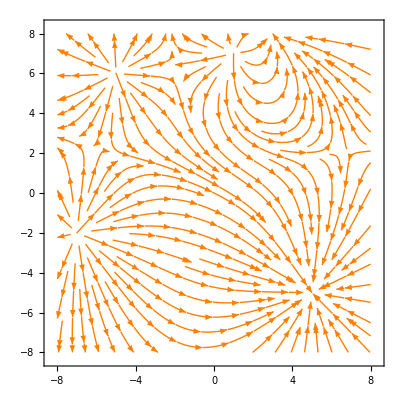

```mathematica
CampoEG=StreamPlot[CampoE,{x,-lg,lg},{y,-lg,lg},StreamStyle->Orange]
```

Gráfico final con todo junto

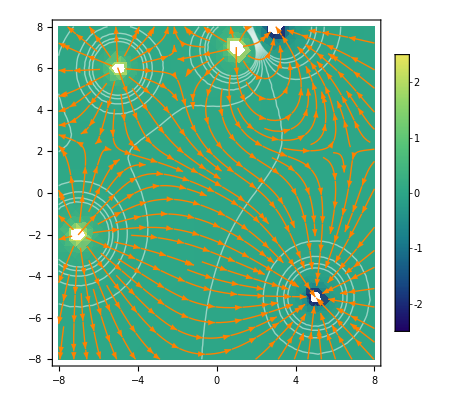

```mathematica
Show[PEHeatG,PECP,CampoEG]
```